### Consider a rectangular workspace with walls that have friction : a robot incontact with the wall is slowed.

#### Draw it

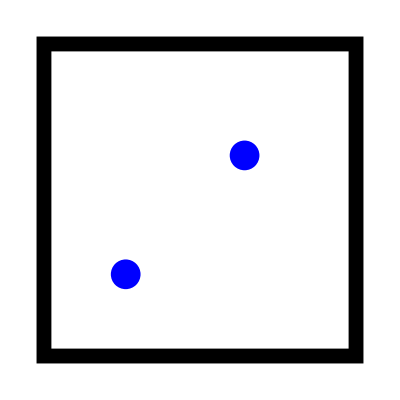

```mathematica
w = 10;
Graphics[{
Black, Rectangle[w*1.1*{-1,-1},w*1.1*{1,1}],
White, Rectangle[w*{-1,-1},w*{1,1}],
(*add robots*)
Blue,
Disk[{3,3},1],
Disk[{-5,-5},1]
}]
```

#### Equations of Motion: assume inputs are velocity (so we have a kinematic, not a dynamic model)

```mathematica
FrictionModel[force_, fricForce_]:= If[Abs[fricForce]>Abs[force],0,force-fricForce]
MotionModel[x_,y_,μFric_, vx_,vy_, TopW_,RightW_,BottomW_,LeftW_ ,RobRadius_]:=(
θ = ArcTan[vx,vy];
If[y≥TopW-RobRadius  && vy > 0,
vy = 0; vx = vx* FrictionModel[Cos[θ],-μFric Sin[θ]]];
If[y≤BottomW+RobRadius  && vy < 0,
vy = 0; vx = vx*FrictionModel[Cos[θ],-μFric Sin[θ]]];
If[x≥RightW-RobRadius  && vy > 0,
vx = 0; vy = vy*FrictionModel[Sin[θ],-μFric Cos[θ]]];
If[x≤BottomW+RobRadius  && vy < 0,
vx = 0; vy = vy*FrictionModel[Sin[θ],-μFric Cos[θ]]];
(*apply velocity to motion*)
{vx,vy}
)
```

#### Assume leftmost robot is touching left wall. What [vx, vy] should we apply for 1 second to achieve a desired ΔY?

```mathematica
Clear[w]
DSolve[
{
{vx,vy}=MotionModel[x[t],y[t],μFric, vxIn,vyIn, w,w,-w,-w,1];
x'[t]== vx,
y'[t]==vy,y[0]==0,x[0]==-w},
{x,y},t]
```

{{x→Function[{t},t vxIn-w],y→Function[{t},t vyIn]}}

#### A demonstration

```mathematica
MotionModel[x,y,μFric, vxIn,vyIn, w,w,-w,-w,1]
```

{vxIn,vyIn}